```mathematica
f[x_,y_]:=Sin[x]+x y/4+y^2/4;
Plot3D[f[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1},Mesh->False,BoxRatios->Automatic]
```

-Graphics3D-

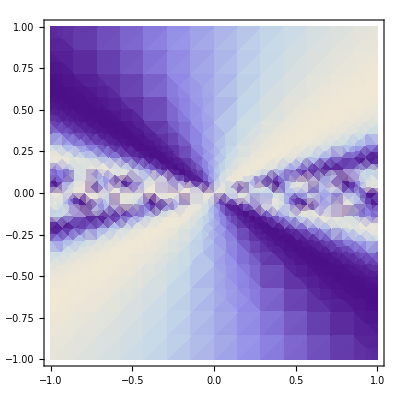

```mathematica
f[x_,y_]:=Sin[x/y];
DensityPlot[f[x,y],{x,-1,1},{y,-1,1}]
```

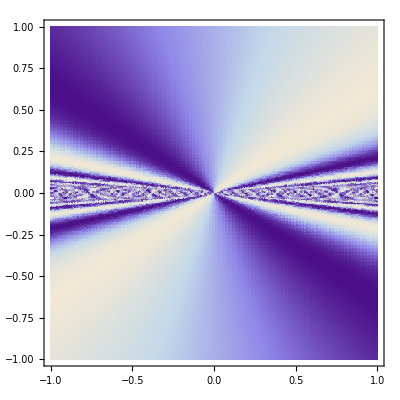

```mathematica
DensityPlot[f[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
Plot3D[f[x,y],{x,-0.1,0.1},{y,-0.1,0.1},PlotPoints->20]
Animate[Plot[f[x,y],{y,-0.01,0.01},PlotPoints->200],{x,-0.1,0.1,0.01}]
```

-Graphics3D-

```mathematica
ContourPlot[Sin[x]+Cos[y],{x,-10,10},{y,-10,10}]
```

-Graphics-

```mathematica
ParametricPlot3D[{Sin[theta]*Cos[phi],Sin[theta]*Sin[phi],Cos[theta]},{theta,0,2 Pi},{phi,0,Pi},Boxed->True,Axes-> True ]
```

-Graphics3D-

```mathematica
f[theta_,phi_]:={Sin[theta] Sin[phi],Sin[theta] Cos[phi],Cos[theta]};
g[x_,y_]:={Cos[phi]+3/4,Sin[phi],theta-Pi/2};
ParametricPlot3D[{f[theta,phi],g[theta,phi]},{theta,0,Pi},{phi,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[f[theta,phi],{theta,3/5 Pi,Pi 4/5},{phi,3/5,3.01/5 Pi}]
```

-Graphics3D-